```mathematica
homogeneous2Cartesian[list_]:=Table[{list[[i,2]],list[[i,3]]}/list[[i,1]],{i,1,Length[list]}](*transform all points in list from homogeneous to Cartesian coordinates*)
```

```mathematica
computeWSPoints[d_,plotQ_]:=Module[{w0,w1,w2,V0,V1,V2,lines,pointsAll,pointsReal,pointsCartesian,pointsInside,pointsTallied,maxNr,pointsMax,Qd},
w0={1,0,0};(*homogeneous coordinates of point w0*)
w1={1,d,0};(*homogeneous coordinates of point w1*)
w2={1,0,d};(*homogeneous coordinates of point w1*)
V0=Table[(w1*i+w0*(d-i))/d,{i,1,d}];(*homogeneous coordinates of all points on e0*)
V1=Table[(w2*i+w1*(d-i))/d,{i,1,d}];(*homogeneous coordinates of all points on e1*)
V2=Table[(w0*i+w2*(d-i))/d,{i,1,d}];(*homogeneous coordinates of all points on e2*)
lines=Flatten[Join[
Table[Cross[V0[[i]],V1[[j]]],{i,1,d-1},{j,1,d}](*homogeneous coordinates of all lines connecting points vi on e0 and vj on e1*),
Table[Cross[V1[[i]],V2[[j]]],{i,1,d-1},{j,1,d}](*homogeneous coordinates of all lines connecting points vi on e1 and vj on e2*),
Table[Cross[V2[[i]],V0[[j]]],{i,1,d-1},{j,1,d}](*homogeneous coordinates of all lines connecting points vi on e2 and vj on e0*)
],1];(*the homogeneous coordinates of a line through points p and q is the cross product of the two homogeneous coordinate vectors of the points*)
pointsAll=Flatten[Table[Table[Cross[lines[[i]],lines[[j]]],{i,1,j-1}],{j,2,Length[lines]}],1];(*homogeneous coordinates of intersection points of all pairs of lines with unique counting; the homogeneous coordinates of the intersection point of two lines is the cross product of the two homogeneous coordinate vectors of the lines*)
pointsReal=Select[pointsAll,#[[1]]=!=0&];(*select only those points that are real (not at infinity)*)
pointsCartesian=homogeneous2Cartesian[pointsReal];(*transform intersection points to Cartesian coordinates*)
pointsInside=Select[pointsCartesian,(Sign[Det[{w0,w1,Prepend[#,1]}]]>0&&Sign[Det[{w1,w2,Prepend[#,1]}]]>0&&Sign[Det[{w2,w0,Prepend[#,1]}]]>0)&];(*select those points inside the triangle w0,w1,w2*)
pointsTallied=SortBy[Tally[pointsInside],Last];
(*Tally all points inside the triangle; the resulting number is the number of pairs of lines that intersect at the point*)
(*if k lines go through a point, then there are n=k*(k-1)/2 distinct pairs that yield the point; we then have k = 1/2 (1+√(1+8 n))*)
maxNr=pointsTallied[[-1,2]];(*maximum number of pairs, maxNr = Q(d)*(Q(d)-1)/2*)
Qd=(Sqrt[maxNr*8+1]+1)/2;(*this is Q(d) = 1/2 (1+√(1+8 maxNr))*)
Print["Case d = ",d,":"];
Print["Q(",d,") = ",Qd];
If[plotQ,
pointsMax=Select[pointsTallied,#[[2]]==maxNr&][[All,1]];Print[pointsMax];(*all points which are contained in Q(d) lines*)
Print[Show[
Graphics[{Black,Line[homogeneous2Cartesian[{w0,w1,w2,w0}]],
Gray,Line[Flatten[Join[
Table[homogeneous2Cartesian[{V0[[i]],V1[[j]]}],{i,1,d-1},{j,1,d}],
Table[homogeneous2Cartesian[{V1[[i]],V2[[j]]}],{i,1,d-1},{j,1,d}],
Table[homogeneous2Cartesian[{V2[[i]],V0[[j]]}],{i,1,d-1},{j,1,d}]
],1]],Red,Table[Disk[pointsMax[[i]],0.05],{i,1,Length[pointsMax]}]}],PlotRange->All]];
];
]
```

Case d = 2:

Q(2) = 3

{{2/3,2/3}}

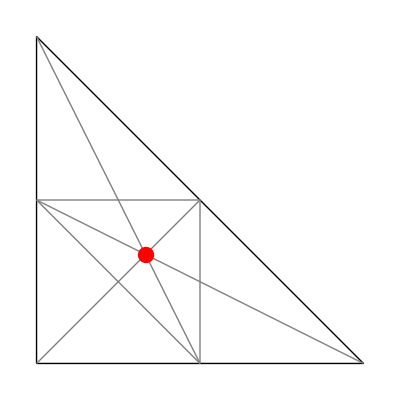

---

Case d = 3:

Q(3) = 3

{{1/2,1},{1/2,3/2},{1,1/2},{1,1},{1,3/2},{3/2,1/2},{3/2,1}}

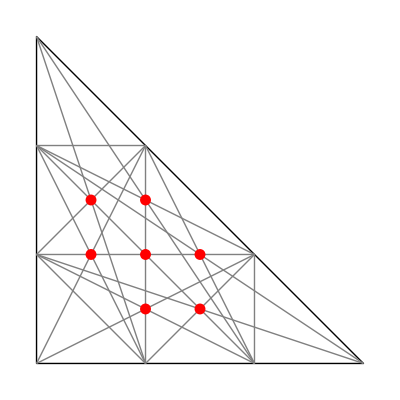

---

Case d = 4:

Q(4) = 4

{{1,1},{1,3/2},{1,2},{3/2,1},{3/2,3/2},{2,1}}

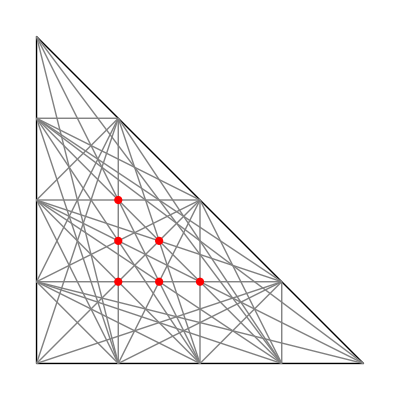

---

Case d = 5:

Q(5) = 5

{{1,2},{2,1},{2,2}}

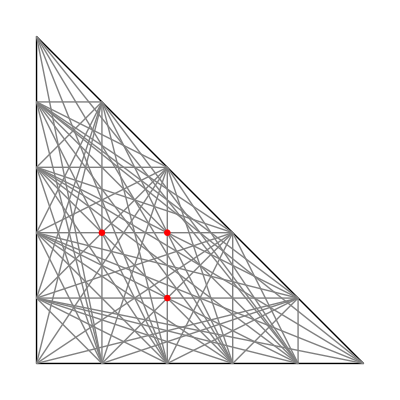

---

Case d = 6:

Q(6) = 6

{{2,2}}

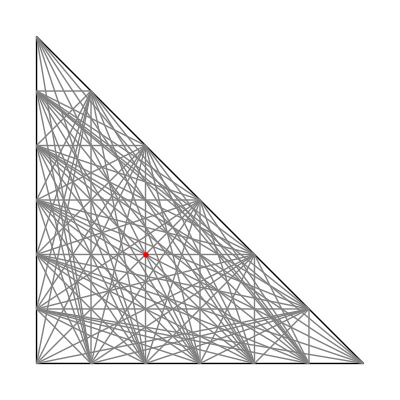

---

Case d = 7:

Q(7) = 7

{{2,2},{2,3},{3,2}}

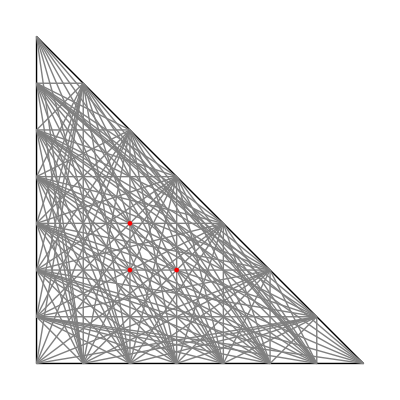

---

Case d = 8:

Q(8) = 6

{{1,3},{1,4},{2,2},{2,3},{2,4},{3,1},{3,2},{3,3},{3,4},{4,1},{4,2},{4,3}}

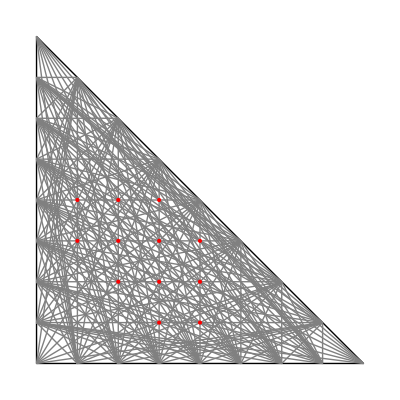

---

Case d = 9:

Q(9) = 8

{{2,3},{2,4},{3,2},{3,4},{4,2},{4,3}}

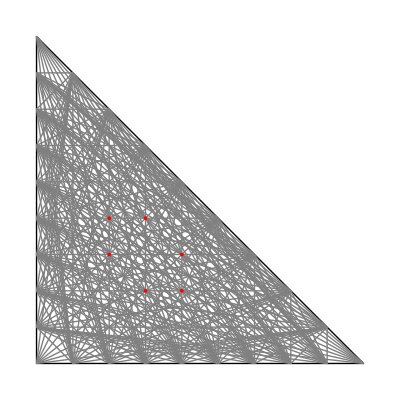

---

Case d = 10:

Q(10) = 8

{{2,2},{2,6},{3,3},{3,4},{4,3},{6,2}}

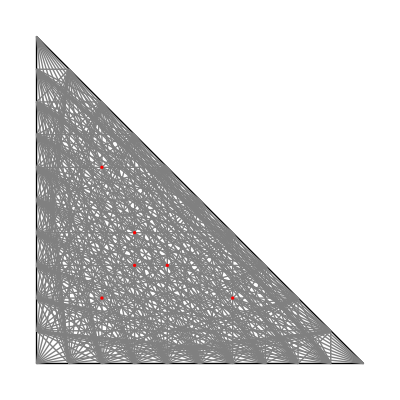

---

Case d = 11:

Q(11) = 9

---

Case d = 12:

Q(12) = 9

---

Case d = 13:

Q(13) = 10

---

Case d = 14:

Q(14) = 10

---

Case d = 15:

Q(15) = 10

---

Case d = 16:

Q(16) = 12

---

Case d = 17:

Q(17) = 11

---

Case d = 18:

Q(18) = 12

---

Case d = 19:

Q(19) = 12

---

Case d = 20:

Q(20) = 12

---

```mathematica
Module[{i},
For[i=2,i≤20,i++,
computeWSPoints[i,If[i≤10,True,False]];
Print["---"];
]
]
```

```mathematica
Module[{i},
For[i=21,i≤40,i++,
computeWSPoints[i,If[i≤10,True,False]];
Print["---"];
]
]
```

Case d = 21:

Q(21) = 13

---

Case d = 22:

Q(22) = 14

---

Case d = 23:

Q(23) = 13

---

Case d = 24:

Q(24) = 14

---

Case d = 25:

Q(25) = 14

---

Case d = 26:

Q(26) = 14

---

Case d = 27:

Q(27) = 15

---

Case d = 28:

Q(28) = 16

---

Case d = 29:

Q(29) = 17

---

Case d = 30:

Q(30) = 16

---

Case d = 31:

Q(31) = 17

---

Case d = 32:

Q(32) = 16

---

Case d = 33:

Q(33) = 17

---

Case d = 34:

Q(34) = 18

---

Case d = 35:

Q(35) = 17

---

Case d = 36:

Q(36) = 18

---

Case d = 37:

Q(37) = 18

---

Case d = 38:

Q(38) = 19

---

Case d = 39:

Q(39) = 19

---

Case d = 40:

Q(40) = 19

---

```mathematica
Module[{i},
For[i=41,i≤60,i++,
computeWSPoints[i,If[i≤10,True,False]];
Print["---"];
]
]
```

Case d = 41:

Q(41) = 18

---

Case d = 42:

Q(42) = 18

---

Case d = 43:

Q(43) = 20

---

Case d = 44:

Q(44) = 20

---

Case d = 45:

Q(45) = 18

---

Case d = 46:

Q(46) = 22

---

Case d = 47:

Q(47) = 20

---

Case d = 48:

Q(48) = 19

---

Case d = 49:

Q(49) = 20

---

Case d = 50:

Q(50) = 21

---

Case d = 51:

Q(51) = 21

---

Case d = 52:

Q(52) = 21

---

Case d = 53:

Q(53) = 22

---

Case d = 54:

Q(54) = 22

---

Case d = 55:

Q(55) = 21

---

Case d = 56:

Q(56) = 23

---

Case d = 57:

Q(57) = 22

---

Case d = 58:

Q(58) = 22

---

Case d = 59:

Q(59) = 21

---

Case d = 60:

Q(60) = 21

---